# Chapter 6 - Problem 4

This problem is very similar to the last one except our periodic structure is different. So let’s, again, define our needed functions, variables and let’s build the structure from those constants.

## Part I. Constants, Variables, and Functions

PP and PI Matrix Functions

```mathematica
Clear["Global`*"];
(* The usual PI and PP matrix functions. This time written a little more elegantly.*)
PI[kL_,kR_] = 
MatrixExp[1/2 * Log[kL/kR] * (PauliMatrix[1] - IdentityMatrix[2])];
PP[kx_,l_]= MatrixExp[-I* kx *l *PauliMatrix[3]];
```

Constants and Conversion Factors

```mathematica
h = 6.62607004 * 10^(-34) ;(* planck's constant *)
m = 9.10938 * 10^(-31); (* planck's constant *)
ℏ = h/(2*Pi);
e = 1.60217 * 10 ^(-19); (* 1 electron volt (ev) = e Joules *)
nano = 1 *10^(-9);
alpha = √((2*m*e)/ℏ^2) * nano;
```

Given Information

```mathematica
V1 = 2; (* Corresponds to length a *)
V2 = 0.5*V1; (* corresponds to length b*)
a = 0.15;
b = 0.05;
c = 0.025;
ka = alpha * √(epi - V1);
kb = alpha  * √(epi - V2);
kc = alpha * √epi;
numofperiods = 3; (* This is the number of times this structure repeats. We've kept it constant throughout all of chapter 6*)
```

## Part II. The Transfer Matrix

This system is very much like the last one. We need to build one period carefully, double check it, then triple check that we built it correctly. Then use matrix power to repeat it for the specified number of periods (numofperiods variable). Here is an image of the structure so that we don’t have to scroll up.
-Graphics-
We can see that the left and right side of the periodic structure are actually NOT the same. We can’t do what we did last time where we split it into side products and center products. We actually have to write out the full TransferMatrix PP and PI multiplication. BE CAREFUL!

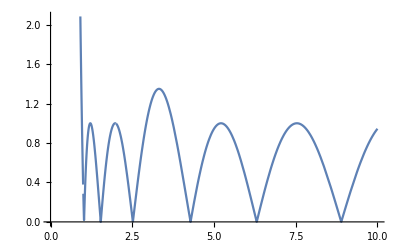

```mathematica
TransferMatrix = PP[kc, c].PI[kc, kb].PP[kb,b].PI[kb,kc].PP[kc,b].PI[kc,ka].PP[ka,a]. PI[ka,kc].PP[kc,b].PI[kc,kb].PP[kb,b].PI[kb,kc].PP[kc,c];
TransferMatrix = MatrixPower[TransferMatrix,numofperiods];
Subscript[P, 11] = Tr[TransferMatrix]/2;
TransferPlot= Plot[Abs[Subscript[P, 11]],{epi, 0,10}]
```

## Part III. The Forbidden Bands

This part is very similar in all the problems across chapter 6. We will draw a line at 1 and see when it crosses. And just to double check, we will shift the whole graph down by 1. Then we will use the “Get Coordinates” feature  of Mathematica to estimates the roots, then FindRoot function to find the exact roots. The area between each of the roots will be our Forbidden bands.

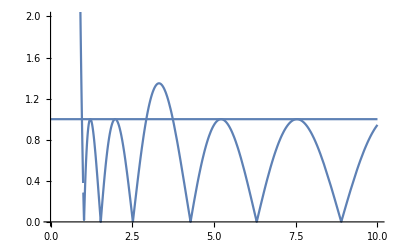

```mathematica
LineAtOne = Plot[1,{epi,0,10}];
Show[LineAtOne,TransferPlot]
```

Wow shit, the transfer function barely touches the 1 line. Let’s see if those little touches are zeros by shifting it to the axis...if that even helps.

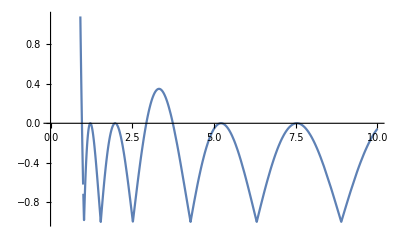

```mathematica
TransferPlot2 = Plot[Abs[Subscript[P, 11]] - 1,{epi,0,10}]
```

```mathematica
NumOfRoots = 10; (* There definitely 11 roots...but we gotta keep this number even for now*)
Array[ForbiddenRoots,NumOfRoots]; (* let's store our answers in an array.*)
Array[StartSearch, NumOfRoots];
(* our guesses as to where the roots are*)
StartSearch[1] = 1.1;
StartSearch[2] = 1.2;
StartSearch[3] = 1.8;
StartSearch[4] = 1.9;
StartSearch[5] = 2.7;
StartSearch[6] = 3.7;
StartSearch[7] = 5.0;
StartSearch[8] = 5.2;
StartSearch[9] = 7.4;
StartSearch[10] = 7.6;
For[i = 1,i≤ NumOfRoots, i++,
ForbiddenRoots[i] = epi/.FindRoot[Abs[Subscript[P, 11]]==1,{epi,StartSearch[i]}];]
For[i = 1, i ≤NumOfRoots , i+= 2,
Print["Forbidden band from \n\t", ForbiddenRoots[i], " eV to ", ForbiddenRoots[i+1], " eV"]]
```

Forbidden band from 
	1.2171 eV to 1.2171 eV

Forbidden band from 
	1.97728 eV to 1.97728 eV

Forbidden band from 
	2.93002 eV to 3.74121 eV

Forbidden band from 
	5.21487 eV to 5.21487 eV

Forbidden band from 
	7.53574 eV to 7.53574 eV

Uhm. I’m unsure about this answer since you can see that some of the forbidden bands happen for a singular energy value. However, the rest of the forbidden bands seem correct.
Band #1, #4 and #5 is singular. This might be a problem.